```mathematica
dataB=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/334/B.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataB//TableForm
```

```mathematica
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
forTeXB=MapAt[dropLastDot@*ToString,dataB,{{2;;,All}}];
forTeXB//TeXForm
```

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
myTicksX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.2}]
myTicksY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.2}]
```

```mathematica
forFit=(*Select[*)dataB⟦2;;,{2,6}⟧(*,First@#>22&]*);
fit=LinearModelFit[forFit(*⟦All,;;2⟧*),{x,1},x];
forFit
fit@"ParameterTable"
fit@"Function"
```

{{0.3,0.19},{0.5,0.31},{0.7,0.43},{0.9,0.53},{1.2,0.69},{1.5,0.8},{1.8,0.86},{2.06,0.92}}

| Estimate | Standard Error | t-Statistic | P-Value
x | 0.418802 | 0.0311438 | 13.4473 | 0.0000104775
1 | 0.122192 | 0.0394151 | 3.10012 | 0.0211133

0.122192+0.418802 #1&

```mathematica
f[a_][x_]:=a*x^2;
fitting@data_:=
Module[{
start=data⟦MaximalBy[FindPeaks@data⟦All,2⟧,#⟦2⟧&]⟦1,1⟧⟧,
nlm,a,x},

nlm=
NonlinearModelFit[
data,
f[a][x],
{
{a,start⟦2⟧}
{x0,start⟦1⟧},
{b,√(#2^2/(4#3^2)-#1/#3//RealAbs)&@@CoefficientList[Fit[data,{1,x,x^2},x],x]}
},x,
Weights->data⟦All,2⟧^4];

Print[nlm@"ParameterTable"/.Thread[{a}->{"a"}]];
nlm@"Function"
](*end of fitting definition*)
```

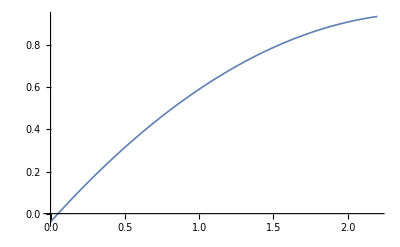

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.250637 | 0.0225556 | 11.112 | 0.0000106338

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.250637 | 0.0225556 | 11.112 | 0.0000106338

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.250637 | 0.0225556 | 11.112 | 0.0000106338

```mathematica
dataForFit=dataB⟦2;;,{2,6}⟧;
fitDataB=Fit[dataForFit,{1,x,x^2},x];
Plot[fitDataB,{x,0,2.2}, PlotStyle->Thickness@0.003]
```

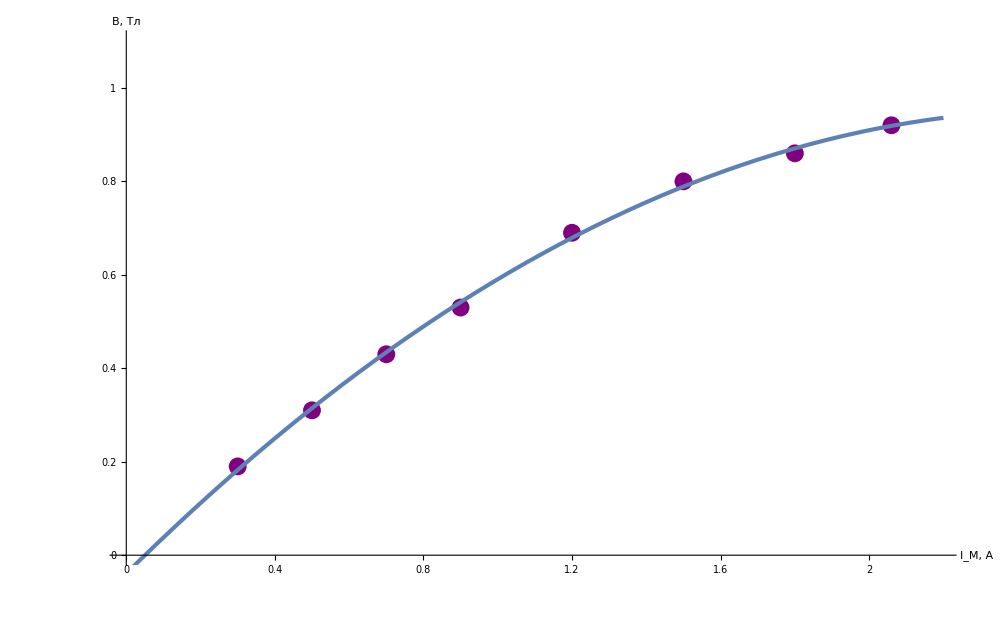

```mathematica
Show[ListPlot[dataB⟦2;;,{2,6}⟧,
GridLines->{grids@0.2,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"I_M, A","B, Тл"},
AxesStyle->Directive[Large,Black],
PlotStyle->{Thickness@0.003 ,Purple},
Ticks->{myTicksX, myTicksY}, 
PlotRange->{{0,2.19},{0,1.1}},
ImageSize->1000], Plot[fitDataB,{x,0,2.2}, PlotStyle->Thickness@0.003]]
```

```mathematica
dataU=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/334/U.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
forTeXU=MapAt[dropLastDot@*ToString,dataU,{{2;;,All}}];
forTeXU//TeXForm
```

```mathematica
dataE=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/334/E.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
forTeXE=MapAt[dropLastDot@*ToString,dataE,{{2;;,All}}];
forTeXE//TeXForm
```

StringTake::take: Cannot take positions -1 through -1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

\left(
\begin{array}{cccccccccc}
 \text{N} & \text{Im, A} & 0.22 & 0.35 & 0.5 & 0.6 & 0.7 & 0.85 & 1.07 & 1.07 \\
 \text{} & \text{} & \text{U} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 1 & 0.1 & -8 & -10 & -14 & -16 & -20 & -25 & -29 & -28 \\
 2 & 0.3 & -19 & -31 & -45 & -54 & -62 & -75 & -96 & -94 \\
 3 & 0.6 & -38 & -62 & -89 & -106 & -127 & -152 & -188 & -192 \\
 4 & 0.9 & -55 & -87 & -122 & -151 & -173 & -209 & -262 & -277 \\
 5 & 1.2 & -68 & -106 & -151 & -183 & -213 & -256 & -324 & -342 \\
 6 & 1.5 & -76 & -120 & -169 & -205 & -239 & -289 & -364 & -389 \\
 7 & 1.8 & -82 & -128 & -191 & -219 & -257 & -310 & -389 & -418 \\
 8 & 2.1 & -86 & -134 & -190 & -229 & -268 & -321 & -404 & -434 \\
\end{array}
\right)

```mathematica
dataR=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/334/R.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
forTeXR=MapAt[dropLastDot@*ToString,dataR,{{2;;,All}}];
forTeXR//TeXForm
```

StringTake::take: Cannot take positions -1 through -1 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

\left(
\begin{array}{cccccccccc}
 \text{N} & \text{B} & 0.22 & 0.35 & 0.5 & 0.6 & 0.7 & 0.85 & 1.07 & 1.07 \\
 \text{} & \text{} & \text{U} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 1 & 0.17 & 4.7 & 3.7 & 3.6 & 3.5 & 3.7 & 3.8 & 3.5 & 3.4 \\
 2 & 0.19 & 10 & 10.3 & 10.4 & 10.4 & 10.3 & 10.2 & 10.4 & 10.2 \\
 3 & 0.37 & 10.3 & 10.5 & 10.6 & 10.5 & 10.8 & 10.6 & 10.4 & 10.7 \\
 4 & 0.53 & 10.4 & 10.3 & 10.1 & 10.4 & 10.3 & 10.2 & 10.2 & 10.7 \\
 5 & 0.69 & 9.9 & 9.7 & 9.6 & 9.7 & 9.7 & 9.6 & 9.7 & 10.2 \\
 6 & 0.8 & 9.5 & 9.4 & 9.3 & 9.4 & 9.4 & 9.4 & 9.4 & 10 \\
 7 & 0.86 & 9.5 & 9.4 & 9.8 & 9.3 & 9.4 & 9.3 & 9.3 & 10 \\
 8 & 0.92 & 9.3 & 9.2 & 9.1 & 9.1 & 9.2 & 9 & 9 & 9.7 \\
\end{array}
\right)